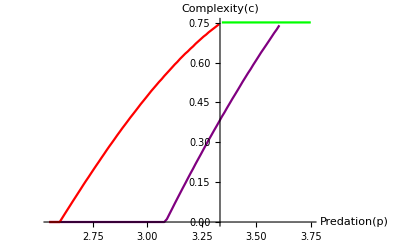

```mathematica
(*This notebook produces the results for Figure 3 in the main text. The first cell simply uses the formulae in Section S5 of the Supplemental material. The second cell finds the outlier eigenvalues and tests whether the origin is inside the bulk for various values of q.  Both cells produce the same stability diagram but the first is much faster. This verifies two things -- (1) we see only a stationary Turing instability, (2) If the bulk does not cross the imaginary axis for q = 0, it doesn't for q ≠ 0. For different sets of system parameters, point (1) may not be true, but we have not found any sets of system parameters for which point (2) is untrue. *)
Clear["Global`*"];

(*Model parameters*)
(*Fraction of the community prey/predator*)
gammafracu = 2.0/3.0;
gammafracv = 1.0/3.0;
(*intra-species interaction strengths*)
du = 1.0;
dv = 1.0;
(*Mean inter-species interctions (multipled by the connectance and total number of species)*)
ncmuuu =3.0;
ncmuvv = -1.5;
(*Asymmetry parameters*)
gammau = 0.5;
gammav = -0.9;
gammauv = -0.5;
(*Dispersal coeffcients*)
ddu = 1.0;
ddv =5.0;

(*The range of Sqrt[complexity] over which to search for the point of instability*)
sqrtcompmin = 0.0;
sqrtcompmax =Sqrt[0.8];
numsqrtcomp = 1001;
sqrtcompvec = Table[x, {x, sqrtcompmin, sqrtcompmax, (sqrtcompmax - sqrtcompmin)/(numsqrtcomp-1)}];

(*The range of ncmuuv to search for the point of instability*)
ncmuuvmin = 2.55;
ncmuuvmax = 3.75;
nummu = 101;
ncmuuvvec = Table[x, {x, ncmuuvmin, ncmuuvmax, (ncmuuvmax - ncmuuvmin)/(nummu-1)}];

(*To store the critical points*)
critsqrtcompbulk = Table[0, {x,nummu}];
critsqrtcompq0= Table[0, {x,nummu}];
critsqrtcompturing= Table[0, {x,nummu}];


(*For various values of mu find the critical values of complexity*)
Monitor[
For[k = 1, k<nummu+1, k++, 
ncmuuv = -ncmuuvvec[[k]];
ncmuvu = ncmuuvvec[[k]];



flagbulk= 0;
flagdet = 0;
flagturing =0;
j = 1;
While[ flagbulk ==0 && flagdet == 0  && j<numsqrtcomp +1,
complexity = sqrtcompvec[[j]]^2;
sqrtcomp = Sqrt[complexity];


(*First find the integrated response functions*)
chiu0 = 0.1;
chiv0 = 0.1;
chiuy0 = 0.1;
chivx0 = 0.1;
qminsq0 = 0.1;

flag1 = 0;
flag2 = 0;
flag3 = 0;


s = FindRoot[{-(du ) mychiu + gammafracu complexity gammau mychiu^2 + gammafracv complexity gammauv mychiv mychiu ==-1,  -(dv ) mychiv  + gammafracu complexity gammauv mychiu mychiv + gammafracv complexity gammav mychiv^2  ==-1},{{mychiu, chiu0 }, {mychiv,chiv0 }}];

{chiu, chiv} ={mychiu, mychiv}  /. s ;


(*Now test if various stability criteria are satisfied*)
(* Bulk crosses imaginary axis for q = 0 -- see Eq. (S83)*)
bulkcond = gammafracu chiu^2 + gammafracv chiv^2 - 1/complexity;
If[ bulkcond>0, flag2 = 1;];
If[ flag2==1&& flagbulk ==0, flagbulk =1;critsqrtcompbulk[[k]]=sqrtcomp; ];

flagnonzero =0;
flagzero = 0;
(* Outlier crosses for q = 0 -- see Eq. (S89) *)
outliercond  =( gammafracu ncmuuu - 1/chiu)(gammafracv ncmuvv - 1/chiv)- gammafracu gammafracv ncmuuv ncmuvu ;
If[outliercond<0, flagzero = 1; flagdet = 1;critsqrtcompq0[[k]]=sqrtcomp;  ];



(*Outlier crosses for q ≠ 0 -- see Eq. (S101)*)
s = FindRoot[{gammafracu ncmuuu mychiu1 (gammafracv ncmuvv mychiv-1)+ gammafracv ncmuvv mychiv1 (gammafracu mychiu ncmuuu -1 ) - gammafracu gammafracv ncmuuv ncmuvu (mychiu mychiv1 + mychiu1 mychiv)  == 0,-(du + myqminsq ddu ) mychiu1 - ddu mychiu+2 gammafracu complexity gammau mychiu mychiu1+ gammafracv complexity gammauv (mychiv1 mychiu + mychiv mychiu1) ==0,  -(dv + myqminsq ddv ) mychiv1  - ddv mychiv + gammafracu complexity gammauv (mychiv1 mychiu + mychiv mychiu1)+ 2 gammafracv complexity gammav mychiv mychiv1 ==0,-(du + myqminsq ddu ) mychiu + gammafracu complexity gammau mychiu^2 + gammafracv complexity gammauv mychiv mychiu ==-1,  -(dv + myqminsq ddv ) mychiv  + gammafracu complexity gammauv mychiu mychiv + gammafracv complexity gammav mychiv^2  ==-1},{{mychiu, chiu0 }, {mychiv,chiv0 },{mychiu1, chiu0 }, {mychiv1,chiv0 }, {myqminsq, qminsq0}}];


{chiu, chiv, chiu1, chiv1, qminsq} ={mychiu, mychiv, mychiu1, mychiv1, myqminsq}  /. s ;

outliercondnonzero = ( gammafracu ncmuuu - 1/chiu)(gammafracv ncmuvv - 1/chiv)- gammafracu gammafracv ncmuuv ncmuvu ;
If[outliercondnonzero<0 , flagnonzero =1; ];
If[flag1==0&&flag2==0&& flagnonzero == 1 &&flagzero ==0 && flagturing ==0,flagturing = 1; critsqrtcompturing[[k]]=sqrtcomp; ];




j = j+1;
];
];
,k];

(*Plotting the results*)

plotpointsbulk= Transpose[{ncmuuvvec, critsqrtcompbulk^2}];
plotpointsq0= Transpose[{ncmuuvvec, critsqrtcompq0^2}];
plotpointsturing = Transpose[{ncmuuvvec, critsqrtcompturing^2}];

flagstartbulk = 0;
deletedbulk = 0;
flagstartturing = 0;
deletedturing = 0;
flagstartq0 = 0;
deletedq0 = 0;
For[k = 1, k<nummu+1, k++, 
If[flagstartbulk == 0 && plotpointsbulk[[k-deletedbulk,2]]≠ 0, flagstartbulk = 1;];
If[flagstartbulk == 0 && plotpointsbulk[[k-deletedbulk,2]]==0, plotpointsbulk=Delete[plotpointsbulk,k-deletedbulk];deletedbulk = deletedbulk +1;];
If[flagstartturing == 0 && plotpointsturing[[k-deletedturing,2]]≠ 0, flagstartturing = 1;];
If[flagstartq0 == 0 && plotpointsq0[[k-deletedq0,2]]≠ 0, flagstartq0= 1;];
If[flagstartturing == 1 && plotpointsturing[[k-deletedturing,2]]==0, plotpointsturing=Delete[plotpointsturing,k-deletedturing];deletedturing= deletedturing +1;];
If[flagstartq0 == 1 && plotpointsq0[[k-deletedq0,2]]==0, plotpointsq0=Delete[plotpointsq0,k-deletedq0];deletedq0= deletedq0 +1;];
];

pltbulk= ListLinePlot[plotpointsbulk, PlotStyle -> Green, PlotRange->All];
pltq0= ListLinePlot[plotpointsq0, PlotStyle -> Red, PlotRange->All];
pltturing = ListLinePlot[plotpointsturing, PlotStyle ->Purple, PlotRange->All];

Show[ pltbulk, pltturing, pltq0, PlotRange-> All, AxesLabel-> {ToExpression["\\mathrm{Predation}(p)",TeXForm,HoldForm],ToExpression["\\mathrm{Complexity}(c)",TeXForm,HoldForm]}]
(*SetDirectory[NotebookDirectory[]];
Export["bulk0.csv",critsqrtcompbulk]
Export["q00.csv",critsqrtcompq0]
Export["turing0.csv",critsqrtcompturing]*)
```

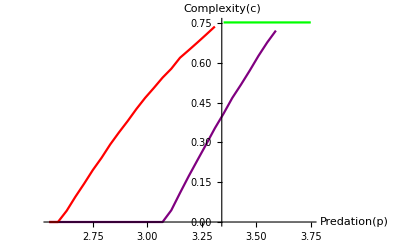

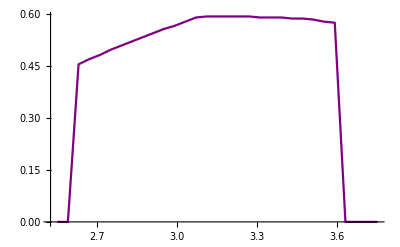

```mathematica
Clear["Global`*"];
(*Model parameters*)
(*Fraction of the community prey/predator*)
gammafracu = 2.0/3.0;
gammafracv = 1.0/3.0;
(*intra-species interaction strengths*)
du = 1.0;
dv = 1.0;
(*Mean inter-species interctions (multipled by the connectance and total number of species)*)
ncmuuu =3.0;
ncmuvv = -1.5;
(*Asymmetry parameters*)
gammau = 0.5;
gammav = -0.9;
gammauv = -0.5;
(*Dispersal coeffcients*)
ddu = 1.0;
ddv =5.0;

(*The range of wavenumbers over which to find the outlier eigenvalues and to test whether the origin is inside the bulk*)
(* The range of is q chosen by running previous trials, observing the range of "qpeak" and narrowing the testing range accordingly.  *)
qmin =0.4; 
qmax =0.7;
numq = 101;
qvec = Table[x,{x, qmin, qmax, (qmax - qmin)/(numq-1)}];
qvec = Prepend[qvec, 0.0];

(*The range of Sqrt[complexity] over which to search for the point of instability*)
sqrtcompmin = 0.0;
sqrtcompmax =Sqrt[0.8];
numsqrtcomp = 201;
sqrtcompvec = Table[x, {x, sqrtcompmin, sqrtcompmax, (sqrtcompmax - sqrtcompmin)/(numsqrtcomp-1)}];

(*The range of ncmuuv to search for the point of instability*)
ncmuuvmin = 2.55;
ncmuuvmax = 3.75;
nummu = 31;
ncmuuvvec = Table[x, {x, ncmuuvmin, ncmuuvmax, (ncmuuvmax - ncmuuvmin)/(nummu-1)}];

(*To store the critical points*)
critsqrtcompbulk = Table[0, {x,nummu}];
critsqrtcompq0= Table[0, {x,nummu}];
critsqrtcompturing= Table[0, {x,nummu}];

(*Store the most unstable vaue of q*)
qpeak= Table[0, {x,nummu}];

(*For various values of mu find the critical values of sqrtcomp*)
Monitor[Monitor[
For[k = 1, k<nummu+1, k++, 
ncmuuv = -ncmuuvvec[[k]];
ncmuvu = ncmuuvvec[[k]];


(*Now test if various stability criteria are satisfied for various sqrtcomp*)
flagbulk= 0;
flagdet = 0;
flagturing =0;
j = 1;
While[flagbulk ==0 && flagdet == 0  && j<numsqrtcomp +1,
complexity = sqrtcompvec[[j]]^2;
sqrtcomp = Sqrt[complexity];


maxoutliervec= Table[0,{x,numq}];

(*First find the integrated response functions*)
chiu0 = 0.1;
chiv0 = 0.1;
chiuy0 = 0.1;
chivx0 = 0.1;


flag1 = 0;
flag2 = 0;
flag3 = 0;

For[i = 1, i<numq+1, i++,
q = qvec[[i]];

(*Calculating the outlier eigenvalues*)
s = NSolve[{-(u + du + q^2 ddu) mychiu + gammafracu complexity gammau mychiu^2 + gammafracv complexity gammauv mychiv mychiu ==-1,  -(u + dv + q^2 ddv) mychiv  + gammafracu complexity gammauv mychiu mychiv + gammafracv complexity gammav mychiv^2  ==-1,  (gammafracu ncmuuu -1/mychiu)(gammafracv ncmuvv -1/mychiv)-(gammafracv ncmuuv)( gammafracu ncmuvu) == 0},{mychiu, mychiv, u}];


eigx = {};
eigy = {};
For[it= 1, it<Length[s]+1, it++,
{chiu, chiv, myu} = {mychiu, mychiv, u}/.s[[it]];
myu1 = gammafracu chiu Conjugate[chiu] + gammafracv chiv Conjugate[chiv]- 1/complexity;
If[Re[myu1]<0,eigx = Append[eigx, Re[myu]];eigy = Append[eigy, Im[myu]];];

];

maxoutliervec[[i]]= Max[eigx];


(* Testing to see if the origin is inside the bulk  *)
s = FindRoot[{-(du + q^2 ddu) mychiu + gammafracu complexity gammau mychiu^2 + gammafracv complexity gammauv mychiv mychiu ==-1,  -(dv + q^2 ddv) mychiv  + gammafracu complexity gammauv mychiu mychiv + gammafracv complexity gammav mychiv^2  ==-1},{{mychiu, chiu0 }, {mychiv,chiv0 }}];

{chiu, chiv} ={mychiu, mychiv}  /. s ;

bulkcond = gammafracu chiu^2 + gammafracv chiv^2 - 1/complexity;
If[ bulkcond>0, flag2 = 1;];




];

flagnonzero =0;
flagzero = 0;
If[maxoutliervec[[1]] >0 , flagzero = 1; flagdet = 1;critsqrtcompq0[[k]]=sqrtcomp;  ];
peak = 1;
For[i=2, i<numq+1, i++,
If[maxoutliervec[[i]]>maxoutliervec[[peak]], peak =i;];
];
If[maxoutliervec[[peak]]>0 && peak >1, flagnonzero =1; ];



If[flag1==0&&flag2==0&& flagnonzero == 1 &&flagzero ==0 && flagturing ==0,flagturing = 1; critsqrtcompturing[[k]]=sqrtcomp; qpeak[[k]] = qvec[[peak]] ;];


If[ flag2==1&& flagbulk ==0, flagbulk =1;critsqrtcompbulk[[k]]=sqrtcomp; ];


j = j+1;
];
];
,k];,j];

(*Plotting the results*)
plotpointspeak = Transpose[{ncmuuvvec, qpeak}];
plotpointsbulk= Transpose[{ncmuuvvec, critsqrtcompbulk^2}];
plotpointsq0= Transpose[{ncmuuvvec, critsqrtcompq0^2}];
plotpointsturing = Transpose[{ncmuuvvec, critsqrtcompturing^2}];

flagstartbulk = 0;
deletedbulk = 0;
flagstartturing = 0;
deletedturing = 0;
flagstartq0 = 0;
deletedq0 = 0;
For[k = 1, k<nummu+1, k++, 
If[flagstartbulk == 0 && plotpointsbulk[[k-deletedbulk,2]]≠ 0, flagstartbulk = 1;];
If[flagstartbulk == 0 && plotpointsbulk[[k-deletedbulk,2]]==0, plotpointsbulk=Delete[plotpointsbulk,k-deletedbulk];deletedbulk = deletedbulk +1;];
If[flagstartturing == 0 && plotpointsturing[[k-deletedturing,2]]≠ 0, flagstartturing = 1;];
If[flagstartq0 == 0 && plotpointsq0[[k-deletedq0,2]]≠ 0, flagstartq0= 1;];
If[flagstartturing == 1 && plotpointsturing[[k-deletedturing,2]]==0, plotpointsturing=Delete[plotpointsturing,k-deletedturing];deletedturing= deletedturing +1;];
If[flagstartq0 == 1 && plotpointsq0[[k-deletedq0,2]]==0, plotpointsq0=Delete[plotpointsq0,k-deletedq0];deletedq0= deletedq0 +1;];
];

pltbulk= ListLinePlot[plotpointsbulk, PlotStyle -> Green, PlotRange->All];
pltq0= ListLinePlot[plotpointsq0, PlotStyle -> Red, PlotRange->All];
pltturing = ListLinePlot[plotpointsturing, PlotStyle ->Purple, PlotRange->All];

Show[ pltbulk,  pltturing,pltq0, PlotRange-> All, AxesLabel-> {ToExpression["\\mathrm{Predation}(p)",TeXForm,HoldForm],ToExpression["\\mathrm{Complexity}(c)",TeXForm,HoldForm]}]
pltpeak = ListLinePlot[plotpointspeak, PlotStyle ->Purple]
(*SetDirectory[NotebookDirectory[]];
Export["bulk1.csv",critsqrtcompbulk]
Export["q01.csv",critsqrtcompdet]
Export["turing1.csv",critsqrtcompturing]*)
```